```mathematica
DifferentialD[Cos[Log[x]]]
```

ⅆCos[Log[x]]

```mathematica
f[x_] = Cos[Log[x]]
```

Cos[Log[x]]

```mathematica
f'[x]
f''[x]
```

-Sin[Log[x]]/x

-Cos[Log[x]]/x^2+Sin[Log[x]]/x^2

```mathematica
g[x_] = Sin[Log[x]]
x^2*g''[x] + x*g'[x] + g[x]
```

Sin[Log[x]]

Cos[Log[x]]+Sin[Log[x]]+x^2 (-Cos[Log[x]]/x^2-Sin[Log[x]]/x^2)

```mathematica
Simplify[%]
```

0

```mathematica
DSolve[{y'[x]==xy[x],y[0]==2},y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,True}.

DSolve[{True,True},y[x],x]

```mathematica
DSolve[y'[z]==zy[z],y[z],z]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument True.

DSolve[True,y[z],z]

```mathematica
DSolve[y'[x]==y[x] + a Sin[x],y[x],x]
```

{{y[x]→-a Sin[x]+xy[x]}}

```mathematica
Clear[Global,"*"]
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear::wrsym will be suppressed during this calculation.

Clear::spsym: Special symbol $ActivationGroupID cannot be cleared.

Clear::spsym: Special symbol $ActivationKey cannot be cleared.

Clear::spsym: Special symbol $ActivationUserRegistered cannot be cleared.

General::stop: Further output of Clear::spsym will be suppressed during this calculation.

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y'[x]==y[x] + a Sin[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]-1/2 a (Cos[x]+Sin[x])}}

```mathematica
PacletInstall@"path/to/downloaded/CellsToTeX-0.2.2.paclet"
```

$Failed

```mathematica
PacletInstall@"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"
```

$Failed

```mathematica
PacletInstall"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"
```

http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet PacletInstall

```mathematica
Import["https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"]
```

$Failed

```mathematica
<<https://paclets.github.io/PacletServer/Install.wl
PublicPacletInstall["CellsToTeX"]
```

Failure[…]

```mathematica
Import@"https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"
```

$Failed

{{y[x]→1/4 ⅇ^x (-1+2 x)+ⅇ^x C[1]+ⅇ^-x C[2]}}

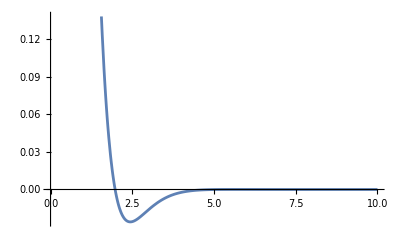
$DisplayFunction[-Graphics-]

```mathematica
y
```

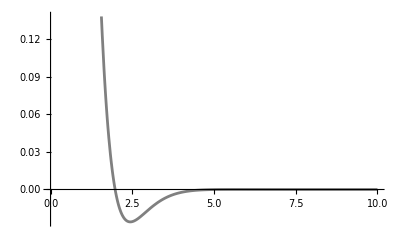
$DisplayFunction[-Graphics-]

```mathematica
Plot[Exp[-2x]*(3Sin[x] + 7Cos[x]),{x,0,10},PlotStyle->Gray]
```

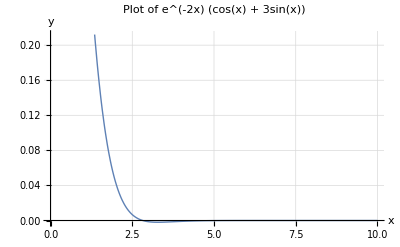
$DisplayFunction[-Graphics-]

```mathematica
Plot[Exp[-2 x] (Cos[x]+3 Sin[x]),{x,0,10},PlotStyle->Thick,AxesLabel->{"x","y"},PlotLabel->"Plot of e^(-2x) (cos(x) + 3sin(x))",GridLines->Automatic]
```

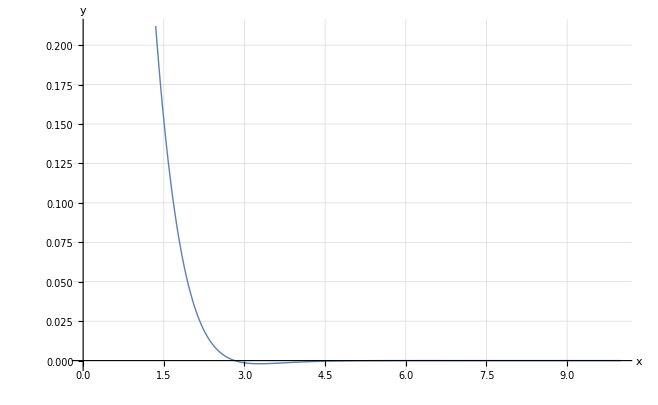

```mathematica
$DisplayFunction=Identity;
Plot[Exp[-2 x] (Cos[x]+3 Sin[x]),{x,0,10},PlotStyle->Thick,AxesLabel->{"x","y"},GridLines->Automatic]
```

```mathematica
Clear[x,y]
```

```mathematica
DSolve[y'[x]^2 +y[x] == 2,y,x]
```

{{y→Function[{x},1/4 (8-x^2-2 x C[1]-C[1]^2)]},{y→Function[{x},1/4 (8-x^2+2 x C[1]-C[1]^2)]}}

```mathematica
Simplify[%]
```

{{y→Function[{x},1/4 (8-x^2-2 x C[1]-C[1]^2)]},{y→Function[{x},1/4 (8-x^2+2 x C[1]-C[1]^2)]}}

```mathematica
DSolve[y''[x]*y'''[x] == 0,y,x]
```

{{y→Function[{x},C[1]+x C[2]]},{y→Function[{x},C[1]+x C[2]+x^2 C[3]]}}

```mathematica
DSolve[y'[x]-y[x]^2 == 1,y,x]
```

{{y→Function[{x},Tan[x+C[1]]]}}

```mathematica
DSolve[y''''[x]==x,y,x]
```

{{y→Function[{x},x^5/120+C[1]+x C[2]+x^2 C[3]+x^3 C[4]]}}

```mathematica
DSolve[y''''[x]-y[x] == x^3,y,x]
```

{{y→Function[{x},-x^3+ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]]}}

```mathematica
Solve[r*(r-1)^2(r-4) + 1 == 0,r]
```

{{r→Root1.52Root[1-4 #1+9 #1^2-6 #1^3+#1^4&,1]1.5153596067063246},{r→Root3.97Root[1-4 #1+9 #1^2-6 #1^3+#1^4&,2]3.971483205255795},{r→Root0.257-0.317 ⅈRoot[1-4 #1+9 #1^2-6 #1^3+#1^4&,3]0.25657859401894034},{r→Root0.257+0.317 ⅈRoot[1-4 #1+9 #1^2-6 #1^3+#1^4&,4]0.25657859401894034}}

```mathematica
Roots[x*(x-1)^2*(x-4) + 1==0,x]
```

x==3/2-1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))-1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)-8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))||x==3/2-1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)-8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))||x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))-1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))||x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))

```mathematica
TeXForm[%]
```

x=\frac{3}{2}-\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}-\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}-\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}\lor x=\frac{3}{2}-\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6
   \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}+\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6
   \sqrt{249}}-\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}-\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6
   \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}}}\lor x=\frac{3}{2}+\frac{1}{2} \sqrt{3+\frac{1}{3}
   \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}-\frac{1}{2} \sqrt{6-\frac{1}{3}
   \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3}
   \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}}}\lor x=\frac{3}{2}+\frac{1}{2}
   \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}+\frac{1}{2}
   \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2-1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))-1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)-8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}-\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}-\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}-\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2-1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)-8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}-\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}+\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}-\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))-1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}+\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}-\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}+\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}+\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}+\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}+\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
JordanDecomposition[{{4,2,1},{0,4,2},{0,0,4}}]
```

{{{1,0,0},{0,1/2,-1/8},{0,0,1/4}},{{4,1,0},{0,4,1},{0,0,4}}}

```mathematica
MatrixForm[%]
```

((1
0
0) | (0
1/2
-1/8) | (0
0
1/4)
(4
1
0) | (0
4
1) | (0
0
4))

```mathematica
JordanDecomposition[{{4,0,0},{2,4,0},{1,2,4}}]
MatrixForm[%]
```

{{{0,0,1/4},{0,1/2,-1/8},{1,0,0}},{{4,1,0},{0,4,1},{0,0,4}}}

((0
0
1/4) | (0
1/2
-1/8) | (1
0
0)
(4
1
0) | (0
4
1) | (0
0
4))

```mathematica
Roots[(2-x)^3*(1-x)*(-1-x) + 10 == 0,x]
```

x==Root-0.702Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,1]-0.7023216420195433||x==Root-0.178Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,2]-0.1775653289792452||x==Root3.06Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,3]3.061092435840131||x==Root1.91-1.26 ⅈRoot[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,4]1.9093972675793283||x==Root1.91+1.26 ⅈRoot[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,5]1.9093972675793283

```mathematica
TeXForm[%]
```

x=\text{Root}\left[\text{$\#$1}^5-6 \text{$\#$1}^4+11 \text{$\#$1}^3-2 \text{$\#$1}^2-12
   \text{$\#$1}-2\&,1\right]\lor x=\text{Root}\left[\text{$\#$1}^5-6 \text{$\#$1}^4+11 \text{$\#$1}^3-2
   \text{$\#$1}^2-12 \text{$\#$1}-2\&,2\right]\lor x=\text{Root}\left[\text{$\#$1}^5-6 \text{$\#$1}^4+11
   \text{$\#$1}^3-2 \text{$\#$1}^2-12 \text{$\#$1}-2\&,3\right]\lor x=\text{Root}\left[\text{$\#$1}^5-6
   \text{$\#$1}^4+11 \text{$\#$1}^3-2 \text{$\#$1}^2-12 \text{$\#$1}-2\&,4\right]\lor
   x=\text{Root}\left[\text{$\#$1}^5-6 \text{$\#$1}^4+11 \text{$\#$1}^3-2 \text{$\#$1}^2-12
   \text{$\#$1}-2\&,5\right]

```mathematica
Roots[(2-x)^3*(1-x)*(-1-x) + 10 == 0,x]
```

x==Root-0.702Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,1]-0.7023216420195433||x==Root-0.178Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,2]-0.1775653289792452||x==Root3.06Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,3]3.061092435840131||x==Root1.91-1.26 ⅈRoot[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,4]1.9093972675793283||x==Root1.91+1.26 ⅈRoot[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,5]1.9093972675793283

```mathematica
Simplify[(x)*(x-1)*(x-2)*(x-3) + 6*x*(x-1)*(x-2) + 9*x*(x-1) + 3*x + 1]
```

(1+x^2)^2

```mathematica
JordanDecomposition[{{27,48,81},{-6,0,0},{1,0,3}}]
```

{{{3,18,2},{-3,-9,-1/4},{1,2,0}},{{6,0,0},{0,12,1},{0,0,12}}}

```mathematica
Map[MatrixForm,%]
```

{(3 | 18 | 2
-3 | -9 | -1/4
1 | 2 | 0),(6 | 0 | 0
0 | 12 | 1
0 | 0 | 12)}

```mathematica
{{6,0,0},{0,12,1},{0,0,12}}.{{6,0,0},{0,12,1},{0,0,12}}
```

{{36,0,0},{0,144,24},{0,0,144}}

```mathematica
Det[{{1,Exp[-4*t],2*Exp[3*t]},{6,2*Exp[-4*t],3*Exp[3*t]},{-13,-Exp[-4*t],2*Exp[3*t]}}]
```

-4 ⅇ^-t

```mathematica
A = {{1,0,2,-1.8,0},{0,5.1,0,-1,3},{1,2,-3,0,0},{0,1,-3.1,4,0},{-2.8,0,0,1.5,1}}
MatrixForm[Eigenvalues[A]]
MatrixForm[Eigenvectors[A]]
```

{{1,0,2,-1.8,0},{0,5.1,0,-1,3},{1,2,-3,0,0},{0,1,-3.1,4,0},{-2.8,0,0,1.5,1}}

(5.05452
4.09561
-2.92362
2.02882
-0.155338)

(-0.0312209 | -0.949058 | -0.239535 | -0.195825 | -0.0508861
-0.280232 | -0.836611 | -0.275304 | 0.176045 | 0.338775
0.262219 | -0.162664 | -0.826218 | -0.346439 | 0.31957
-0.313235 | -0.64181 | -0.31754 | -0.173787 | 0.599108
-0.301294 | 0.466599 | 0.222136 | 0.0534311 | -0.799567)

```mathematica
{eigenvaluesA, eigenvectorsA}=Eigensystem[A]
```

{{5.05452,4.09561,-2.92362,2.02882,-0.155338},{{-0.0312209,-0.949058,-0.239535,-0.195825,-0.0508861},{-0.280232,-0.836611,-0.275304,0.176045,0.338775},{0.262219,-0.162664,-0.826218,-0.346439,0.31957},{-0.313235,-0.64181,-0.31754,-0.173787,0.599108},{-0.301294,0.466599,0.222136,0.0534311,-0.799567}}}

```mathematica
MatrixForm[eigenvectorsA]
MatrixForm[eigenvaluesA]
```

(-0.0312209 | -0.949058 | -0.239535 | -0.195825 | -0.0508861
-0.280232 | -0.836611 | -0.275304 | 0.176045 | 0.338775
0.262219 | -0.162664 | -0.826218 | -0.346439 | 0.31957
-0.313235 | -0.64181 | -0.31754 | -0.173787 | 0.599108
-0.301294 | 0.466599 | 0.222136 | 0.0534311 | -0.799567)

(5.05452
4.09561
-2.92362
2.02882
-0.155338)

```mathematica
eigenvectorsA[[5]]
```

{-0.301294,0.466599,0.222136,0.0534311,-0.799567}

```mathematica
B = {{3,2,4},{2,0,2},{4,2,3}};
CharacteristicPolynomial[B,x]
Roots[0==-CharacteristicPolynomial[B,x],x]
```

8+15 x+6 x^2-x^3

x==-1||x==-1||x==8

Roots[Roots[8+15 x+6 x^2-x^3],x]

```mathematica
JordanDecomposition[{{3,2,4},{2,0,2},{4,2,3}}]
```

{{{-1,-1,2},{0,2,1},{1,0,2}},{{-1,0,0},{0,-1,0},{0,0,8}}}

```mathematica
MatrixForm[%]
```

((-1
-1
2) | (0
2
1) | (1
0
2)
(-1
0
0) | (0
-1
0) | (0
0
8))

```mathematica
CharacteristicPolynomial[{{2,1,2},{3,0,6},{-4,0,-3}},x]
```

-15+x-x^2-x^3

```mathematica
Roots[%==0,x]
```

x==1-2 ⅈ||x==1+2 ⅈ||x==-3

```mathematica
Simplify[%]
```

x==1/3 (5-4/(-71+3 √561)^(1/3)+2 (-71+3 √561)^(1/3))||x==1/3 (5+(2+2 ⅈ √3)/(-71+3 √561)^(1/3)+ⅈ (ⅈ+√3) (-71+3 √561)^(1/3))||x==1/3 (5+(2-2 ⅈ √3)/(-71+3 √561)^(1/3)+(-1-ⅈ √3) (-71+3 √561)^(1/3))

```mathematica
Integrate[Exp[I*k*x]/(x-a),{x,-Infinity,Infinity},PrincipalValue->True]
```

ConditionalExpression[-π MeijerG[{{0},{-1/2}},{{0,0},{-1/2}},-ⅈ a k]+π^(3/2) MeijerG[{{0},{-1/4,1/4}},{{0,0,1/2},{-1/4,1/4}},(a^2 k^2)/4]+1/2 ⅈ Sign[k] (2 CosIntegral[-a Abs[k]] Sin[a Abs[k]]+Cos[a Abs[k]] (π-2 SinIntegral[a Abs[k]])), k∈ℝ&&Re[a]<0&&Im[a]==0]

```mathematica
Apart[(z)/((z^2 - 1)*(z-I)^2*(z+I)^2),z]
```

1/(8 (-1+z))+ⅈ/(8 (-ⅈ+z)^2)-1/(8 (-ⅈ+z))-ⅈ/(8 (ⅈ+z)^2)-1/(8 (ⅈ+z))+1/(8 (1+z))

```mathematica
Simplify[%]
```

z/((-1+z^2) (1+z^2)^2)

```mathematica
Integrate[x/(1 + x^4),{x,0,Infinity}]
```

π/4

```mathematica
Eigensystem[{{1,-4},{2,5}}]
```

{{3+2 ⅈ,3-2 ⅈ},{{-1+ⅈ,1},{-1-ⅈ,1}}}

```mathematica
Eigensystem[{{5,2},{-4,1}}]
```

{{3+2 ⅈ,3-2 ⅈ},{{-1-ⅈ,2},{-1+ⅈ,2}}}

```mathematica
Phi = {{3*Exp[t],Exp[-t]},{4*Exp[t],4*Exp[-t]}}
```

{{3 ⅇ^t,ⅇ^-t},{4 ⅇ^t,4 ⅇ^-t}}

```mathematica
PhiInv = Inverse[Phi]
```

{{ⅇ^-t/2,-ⅇ^-t/8},{-ⅇ^t/2,(3 ⅇ^t)/8}}

```mathematica
PhiInv.{{0}{4*t}}
```

Dot::dotsh: Tensors {{ⅇ^-t/2,-ⅇ^-t/8},{-ⅇ^t/2,(3 ⅇ^t)/8}} and {{0}} have incompatible shapes.

{{ⅇ^-t/2,-ⅇ^-t/8},{-ⅇ^t/2,(3 ⅇ^t)/8}}.{{0}}

```mathematica
PhiInv.{0,4*t}
```

{-1/2 ⅇ^-t t,(3 ⅇ^t t)/2}

```mathematica
Eigensystem[{{2,-1},{3,-2}}]
```

{{-1,1},{{1,3},{1,1}}}

```mathematica
Inverse[{{Exp[t],Exp[-t]},{3*Exp[t],Exp[-t]}}]
```

{{-ⅇ^-t/2,ⅇ^-t/2},{(3 ⅇ^t)/2,-ⅇ^t/2}}

```mathematica
%.{0,4t}
```

{2 ⅇ^-t t,-2 ⅇ^t t}

```mathematica
Inverse[{{2*Exp[t],Exp[2t]},{Exp[t],Exp[2t]}}]
```

{{ⅇ^-t,-ⅇ^-t},{-ⅇ^(-2 t),2 ⅇ^(-2 t)}}

```mathematica
%.{2,Exp[-3t]}
```

{-ⅇ^(-4 t)+2 ⅇ^-t,2 ⅇ^(-5 t)-2 ⅇ^(-2 t)}

```mathematica
Inverse[{{Exp[t],(1/4)*t*Exp[t] + Exp[t]},{-Exp[t],(1/4)*t*Exp[t]-Exp[t]}}]
```

```mathematica
{{(2 ⅇ^(-2 t) (-ⅇ^t+(ⅇ^t t)/4))/t,(2 ⅇ^(-2 t) (-ⅇ^t-(ⅇ^t t)/4))/t},{(2 ⅇ^-t)/t,(2 ⅇ^-t)/t}}
Simplify[%]
%.{1,1}
Simplify[%]
Integrate[%,t]
Simplify[%]
```

{{(2 ⅇ^(-2 t) (-ⅇ^t+(ⅇ^t t)/4))/t,(2 ⅇ^(-2 t) (-ⅇ^t-(ⅇ^t t)/4))/t},{(2 ⅇ^-t)/t,(2 ⅇ^-t)/t}}

{{(ⅇ^-t (-4+t))/(2 t),-(ⅇ^-t (4+t))/(2 t)},{(2 ⅇ^-t)/t,(2 ⅇ^-t)/t}}

{(ⅇ^-t (-4+t))/(2 t)-(ⅇ^-t (4+t))/(2 t),(4 ⅇ^-t)/t}

{-(4 ⅇ^-t)/t,(4 ⅇ^-t)/t}

{-4 ExpIntegralEi[-t],4 ExpIntegralEi[-t]}

{-4 ExpIntegralEi[-t],4 ExpIntegralEi[-t]}

```mathematica
Eigensystem[{{3,2},{-2,-1}}]
```

{{1,1},{{-1,1},{0,0}}}

```mathematica
Eigensystem[{{1,-2},{1,-1}}]
```

{{ⅈ,-ⅈ},{{1+ⅈ,1},{1-ⅈ,1}}}

```mathematica
Inverse[{{Cos[t]-Sin[t],Cos[t] + Sin[t]},{Cos[t],Sin[t]}}]
```

{{Sin[t]/(-Cos[t]^2-Sin[t]^2),(-Cos[t]-Sin[t])/(-Cos[t]^2-Sin[t]^2)},{-Cos[t]/(-Cos[t]^2-Sin[t]^2),(Cos[t]-Sin[t])/(-Cos[t]^2-Sin[t]^2)}}

```mathematica
Simplify[%]
```

{{-Sin[t],Cos[t]+Sin[t]},{Cos[t],-Cos[t]+Sin[t]}}

```mathematica
%.{Tan[t],1}
```

{Cos[t]+Sin[t]-Sin[t] Tan[t],-Cos[t]+2 Sin[t]}

```mathematica
{{Exp[t],Exp[-t]},{3*Exp[t],Exp[-t]}}.{-2*(t*Exp[-t]+Exp[-t]),-2*(t*Exp[t]-Exp[t])}
```

{-2 ⅇ^t (ⅇ^-t+ⅇ^-t t)-2 ⅇ^-t (-ⅇ^t+ⅇ^t t),-6 ⅇ^t (ⅇ^-t+ⅇ^-t t)-2 ⅇ^-t (-ⅇ^t+ⅇ^t t)}

```mathematica
MatrixForm[%]
```

(-2 ⅇ^t (ⅇ^-t+ⅇ^-t t)-2 ⅇ^-t (-ⅇ^t+ⅇ^t t)
-6 ⅇ^t (ⅇ^-t+ⅇ^-t t)-2 ⅇ^-t (-ⅇ^t+ⅇ^t t))

```mathematica
Simplify[%]
```

{-4 t,-4-8 t}

```mathematica
{{2*Exp[t],Exp[2t]},{Exp[t],Exp[2t]}}.{-Exp[-4t] + 2*Exp[-t],2*Exp[-5t]-2*Exp[-2t]}
```

{ⅇ^(2 t) (2 ⅇ^(-5 t)-2 ⅇ^(-2 t))+2 ⅇ^t (-ⅇ^(-4 t)+2 ⅇ^-t),ⅇ^(2 t) (2 ⅇ^(-5 t)-2 ⅇ^(-2 t))+ⅇ^t (-ⅇ^(-4 t)+2 ⅇ^-t)}

```mathematica
MatrixForm[Simplify[%]]
```

(2
ⅇ^(-3 t))

```mathematica
{{Cos[t]-Sin[t],Cos[t] + Sin[t]},{Cos[t],Sin[t]}}.{{Sin[t]-Cos[t] + Log[Sec[t] + Tan[t]]},{-Sin[t]-2Cos[t]}}
```

{{(-2 Cos[t]-Sin[t]) (Cos[t]+Sin[t])+(Cos[t]-Sin[t]) (-Cos[t]+Log[Sec[t]+Tan[t]]+Sin[t])},{(-2 Cos[t]-Sin[t]) Sin[t]+Cos[t] (-Cos[t]+Log[Sec[t]+Tan[t]]+Sin[t])}}

```mathematica
MatrixForm[%]
```

((-2 Cos[t]-Sin[t]) (Cos[t]+Sin[t])+(Cos[t]-Sin[t]) (-Cos[t]+Log[Sec[t]+Tan[t]]+Sin[t])
(-2 Cos[t]-Sin[t]) Sin[t]+Cos[t] (-Cos[t]+Log[Sec[t]+Tan[t]]+Sin[t]))

```mathematica
MatrixForm[Simplify[%]]
```

(-3 Cos[t]^2+Cos[t] (Log[Sec[t]+Tan[t]]-Sin[t])-Sin[t] (Log[Sec[t]+Tan[t]]+2 Sin[t])
-1+Cos[t] (Log[Sec[t]+Tan[t]]-Sin[t]))

```mathematica
Eigensystem[{{3,-1,-1},{1,1,-1},{1,-1,1}}]
```

{{2,2,1},{{1,0,1},{1,1,0},{1,1,1}}}

```mathematica
JordanDecomposition[{{3,-1,-1},{1,1,-1},{1,-1,1}}]
```

{{{1,1,1},{1,0,1},{1,1,0}},{{1,0,0},{0,2,0},{0,0,2}}}

```mathematica
Integrate[Inverse[{{Exp[2t],Exp[2t],Exp[t]},{0,Exp[2t],Exp[t]},{Exp[2t],0,Exp[t]}}].{0,t,2Exp[t]},t]
```

{-ⅇ^(-2 t) (-1/4-t/2),2 ⅇ^-t,ⅇ^-t (-1-t)+2 t}

```mathematica
Simplify[{{Exp[2t],Exp[2t],Exp[t]},{0,Exp[2t],Exp[t]},{Exp[2t],0,Exp[t]}}.%]
```

{1/4 (-3-2 t+8 ⅇ^t (1+t)),(-1+2 ⅇ^t) (1+t),1/4 (-3+(-2+8 ⅇ^t) t)}

```mathematica
MatrixForm[%]
```

(1/4 (-3-2 t+8 ⅇ^t (1+t))
(-1+2 ⅇ^t) (1+t)
1/4 (-3+(-2+8 ⅇ^t) t))

```mathematica
{{Exp[t],1},{0,1}}.Inverse[{{1,1},{0,1}}]
```

{{ⅇ^t,1-ⅇ^t},{0,1}}

```mathematica
Inverse[%]
```

{{ⅇ^-t,ⅇ^-t (-1+ⅇ^t)},{0,1}}

```mathematica
%.{1/t,1/t}
```

{ⅇ^-t/t+(ⅇ^-t (-1+ⅇ^t))/t,1/t}

```mathematica
({{Exp[t],1},{0,1}}.Inverse[{{1,1},{0,1}}]).Integrate[%,t]
```

{ⅇ^t Log[t]+(1-ⅇ^t) Log[t],Log[t]}

```mathematica
Simplify[%]
```

{Log[t],Log[t]}

```mathematica
B = {{2,-2,2,1},{-1,3,0,3},{0,0,4,-2},{0,0,2,-1}}
Eigensystem[B]
```

{{2,-2,2,1},{-1,3,0,3},{0,0,4,-2},{0,0,2,-1}}

{{4,3,1,0},{{-1,1,0,0},{3,1,2,1},{2,1,0,0},{-6,-4,1,2}}}

```mathematica
PhiB = {{-Exp[4t],3Exp[3t],2Exp[t],-6},{Exp[4t],Exp[3t],Exp[t],-4},{0,2Exp[3t],0,1},{0,Exp[3t],0,2}}
PhiBInv = Simplify[Inverse[PhiB]]
TeXForm[MatrixForm[PhiBInv]]
```

{{-ⅇ^(4 t),3 ⅇ^(3 t),2 ⅇ^t,-6},{ⅇ^(4 t),ⅇ^(3 t),ⅇ^t,-4},{0,2 ⅇ^(3 t),0,1},{0,ⅇ^(3 t),0,2}}

{{-1/3 ⅇ^(-4 t),(2 ⅇ^(-4 t))/3,0,ⅇ^(-4 t)/3},{0,0,(2 ⅇ^(-3 t))/3,-1/3 ⅇ^(-3 t)},{ⅇ^-t/3,ⅇ^-t/3,-2 ⅇ^-t,(8 ⅇ^-t)/3},{0,0,-1/3,2/3}}

\left(
\begin{array}{cccc}
 -\frac{1}{3} e^{-4 t} & \frac{2 e^{-4 t}}{3} & 0 & \frac{e^{-4 t}}{3} \\
 0 & 0 & \frac{2 e^{-3 t}}{3} & -\frac{1}{3} e^{-3 t} \\
 \frac{e^{-t}}{3} & \frac{e^{-t}}{3} & -2 e^{-t} & \frac{8 e^{-t}}{3} \\
 0 & 0 & -\frac{1}{3} & \frac{2}{3} \\
\end{array}
\right)

```mathematica
PhiBInvF = Simplify[PhiBInv.{t*Exp[t],Exp[-t],Exp[2t],1}]
TeXForm[MatrixForm[PhiBInvF]]
```

{1/3 ⅇ^(-5 t) (2+ⅇ^t-ⅇ^(2 t) t),1/3 ⅇ^(-3 t) (-1+2 ⅇ^(2 t)),1/3 (ⅇ^(-2 t)+8 ⅇ^-t-6 ⅇ^t+t),1/3 (2-ⅇ^(2 t))}

\left(
\begin{array}{c}
 \frac{1}{3} e^{-5 t} \left(-e^{2 t} t+e^t+2\right) \\
 \frac{1}{3} e^{-3 t} \left(2 e^{2 t}-1\right) \\
 \frac{1}{3} \left(t+e^{-2 t}+8 e^{-t}-6 e^t\right) \\
 \frac{1}{3} \left(2-e^{2 t}\right) \\
\end{array}
\right)

```mathematica
integratedValue = Simplify[Integrate[PhiBInvF,t]]
TeXForm[MatrixForm[integratedValue]]
```

{1/540 ⅇ^(-5 t) (-72-45 ⅇ^t+20 ⅇ^(2 t) (1+3 t)),1/9 ⅇ^(-3 t) (1-6 ⅇ^(2 t)),1/6 (-ⅇ^(-2 t)-16 ⅇ^-t-12 ⅇ^t+t^2),1/6 (-ⅇ^(2 t)+4 t)}

\left(
\begin{array}{c}
 \frac{1}{540} e^{-5 t} \left(20 e^{2 t} (3 t+1)-45 e^t-72\right) \\
 \frac{1}{9} e^{-3 t} \left(1-6 e^{2 t}\right) \\
 \frac{1}{6} \left(t^2-e^{-2 t}-16 e^{-t}-12 e^t\right) \\
 \frac{1}{6} \left(4 t-e^{2 t}\right) \\
\end{array}
\right)

```mathematica
inhomsol = Simplify[PhiB.integratedValue]
TeXForm[MatrixForm[inhomsol]]
```

{-59/12-ⅇ^-t/5-5 ⅇ^(2 t)-4 t+1/27 ⅇ^t (-1-3 t+9 t^2),-95/36-(3 ⅇ^-t)/10-2 ⅇ^(2 t)-(8 t)/3+1/54 ⅇ^t (2+6 t+9 t^2),2/9-(3 ⅇ^(2 t))/2+(2 t)/3,1/9-ⅇ^(2 t)+(4 t)/3}

\left(
\begin{array}{c}
 \frac{1}{27} e^t \left(9 t^2-3 t-1\right)-4 t-\frac{e^{-t}}{5}-5 e^{2 t}-\frac{59}{12} \\
 \frac{1}{54} e^t \left(9 t^2+6 t+2\right)-\frac{8 t}{3}-\frac{3 e^{-t}}{10}-2 e^{2 t}-\frac{95}{36} \\
 \frac{2 t}{3}-\frac{3 e^{2 t}}{2}+\frac{2}{9} \\
 \frac{4 t}{3}-e^{2 t}+\frac{1}{9} \\
\end{array}
\right)

```mathematica
PhiB.{c1,c2,c3,c4}
```

{-6 c4+2 c3 ⅇ^t+3 c2 ⅇ^(3 t)-c1 ⅇ^(4 t),-4 c4+c3 ⅇ^t+c2 ⅇ^(3 t)+c1 ⅇ^(4 t),c4+2 c2 ⅇ^(3 t),2 c4+c2 ⅇ^(3 t)}

```mathematica
P = {{-1,1,1},{-1,0,1},{-1,1,1}}
MatrixPower[P,2]
```

{{-1,1,1},{-1,0,1},{-1,1,1}}

{{-1,0,1},{0,0,0},{-1,0,1}}

```mathematica
MatrixPower[P,3]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
MatrixExp[{{4,2},{3,3}}t]
```

{{(2 ⅇ^t)/5+(3 ⅇ^(6 t))/5,-(2 ⅇ^t)/5+(2 ⅇ^(6 t))/5},{-(3 ⅇ^t)/5+(3 ⅇ^(6 t))/5,(3 ⅇ^t)/5+(2 ⅇ^(6 t))/5}}

```mathematica
m = MatrixExp[{{-3,-1},{2,-1}}t]
TeXForm[MatrixForm[Simplify[m]]]
```

{{ⅇ^(-2 t) Cos[t]-ⅇ^(-2 t) Sin[t],-ⅇ^(-2 t) Sin[t]},{2 ⅇ^(-2 t) Sin[t],ⅇ^(-2 t) Cos[t]+ⅇ^(-2 t) Sin[t]}}

\left(
\begin{array}{cc}
 e^{-2 t} (\cos (t)-\sin (t)) & -e^{-2 t} \sin (t) \\
 2 e^{-2 t} \sin (t) & e^{-2 t} (\sin (t)+\cos (t)) \\
\end{array}
\right)

```mathematica
Inverse[{{1,0,1},{0,1,0},{1,0,-1}}]
```

{{1/2,0,1/2},{0,1,0},{1/2,0,-1/2}}

```mathematica
{{1,0,1},{0,1,0},{1,0,-1}}.{{Exp[2t^3 + t^2],0,0},{0,Exp[t^5],0},{0,0,Exp[2t^3 - t^2]}}.{{1/2,0,1/2},{0,1,0},{1/2,0,-1/2}}
```

{{1/2 ⅇ^(-t^2+2 t^3)+1/2 ⅇ^(t^2+2 t^3),0,-1/2 ⅇ^(-t^2+2 t^3)+1/2 ⅇ^(t^2+2 t^3)},{0,ⅇ^(t^5),0},{-1/2 ⅇ^(-t^2+2 t^3)+1/2 ⅇ^(t^2+2 t^3),0,1/2 ⅇ^(-t^2+2 t^3)+1/2 ⅇ^(t^2+2 t^3)}}

```mathematica
MatrixForm[%]
```

(1/2 ⅇ^(-t^2+2 t^3)+1/2 ⅇ^(t^2+2 t^3) | 0 | -1/2 ⅇ^(-t^2+2 t^3)+1/2 ⅇ^(t^2+2 t^3)
0 | ⅇ^(t^5) | 0
-1/2 ⅇ^(-t^2+2 t^3)+1/2 ⅇ^(t^2+2 t^3) | 0 | 1/2 ⅇ^(-t^2+2 t^3)+1/2 ⅇ^(t^2+2 t^3))

```mathematica
Simplify[%]
```

{{1/2 ⅇ^(t^2 (-1+2 t)) (1+ⅇ^(2 t^2)),0,1/2 ⅇ^(t^2 (-1+2 t)) (-1+ⅇ^(2 t^2))},{0,ⅇ^(t^5),0},{1/2 ⅇ^(t^2 (-1+2 t)) (-1+ⅇ^(2 t^2)),0,1/2 ⅇ^(t^2 (-1+2 t)) (1+ⅇ^(2 t^2))}}

```mathematica
Integrate[Cos[(n/2)*x]*Exp[-x^2],{x,-Infinity,Infinity}]
```

ⅇ^(-n^2/16) √π

```mathematica
Integrate[Cos[x]*Exp[-x^2],{x,-Infinity,Infinity}]
```

(√π)/ⅇ^(1/4)

```mathematica
InverseFourierTransform[Sin[2*k*t],k,x,FourierParameters->{0,1}]
```

ⅈ √(π/2) DiracDelta[2 t-x]-ⅈ √(π/2) DiracDelta[2 t+x]

```mathematica
FourierTransform[Exp[-x^2],x,k,FourierParameters->{0,1}]
```

(ⅇ^(-k^2/4))/(√2)

```mathematica
Integrate[Exp[-x^2]*Exp[I*k*x],{x,-Infinity,Infinity}]
```

ⅇ^(-k^2/4) √π

```mathematica
f[x_,t_] = Integrate[Exp[-(k^2/4) + 2*I*t*k]*Exp[-I*k*x],{k,-Infinity,Infinity}]
D[f[x,t],{t,2}]-4*D[f[x,t],{x,2}]
```

2 ⅇ^(-(-2 t+x)^2) √π

-8 √π (-2 ⅇ^(-(-2 t+x)^2)+4 ⅇ^(-(-2 t+x)^2) (-2 t+x)^2)+2 √π (-8 ⅇ^(-(-2 t+x)^2)+16 ⅇ^(-(-2 t+x)^2) (-2 t+x)^2)

```mathematica
%*1/(2*Pi)
```

1/(2 π)(128 ⅇ^(-(-2 t+x)^2) √π+64 ⅇ^(-(-2 t+x)^2) √π (16 t-8 x) (-2 t+x)+8 √π (-1+8 t^2-8 t x+2 x^2) (-8 ⅇ^(-(-2 t+x)^2)+16 ⅇ^(-(-2 t+x)^2) (-2 t+x)^2))

128 ⅇ^(-(-2 t+x)^2) √π+64 ⅇ^(-(-2 t+x)^2) √π (16 t-8 x) (-2 t+x)+8 √π (-1+8 t^2-8 t x+2 x^2) (-8 ⅇ^(-(-2 t+x)^2)+16 ⅇ^(-(-2 t+x)^2) (-2 t+x)^2)

```mathematica
Simplify[%]
```

8 ⅇ^(-(-2 t+x)^2) √π (-1+8 t^2-8 t x+2 x^2)

```mathematica
Integrate[10*Exp[-x^2]*Exp[I*k*x],{x,-Infinity,Infinity}]
```

10 ⅇ^(-k^2/4) √π

```mathematica
u[x_,t_]=10*Sqrt[Pi]*(1/(2*Pi))*Integrate[Exp[2*I*k*t-(k^2/4)]*Exp[-I*k*x],{k,-Infinity,Infinity}]
```

10 ⅇ^(-(-2 t+x)^2)

```mathematica
u[x,0]
```

10 ⅇ^(-x^2)

```mathematica
D[u[x,t],{t,2}]-4*D[u[x,t],{x,2}]
```

-40 (-2 ⅇ^(-(-2 t+x)^2)+4 ⅇ^(-(-2 t+x)^2) (-2 t+x)^2)+10 (-8 ⅇ^(-(-2 t+x)^2)+16 ⅇ^(-(-2 t+x)^2) (-2 t+x)^2)

```mathematica
Integrate[(5x-x^2)*Sin[n*Pi*x/5],{x,0,5}]
```

-(125 (-2+2 Cos[n π]+n π Sin[n π]))/(n^3 π^3)

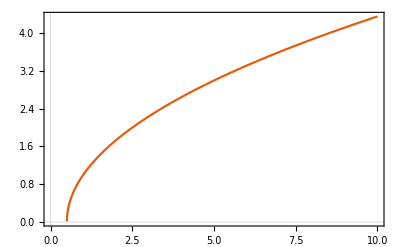

```mathematica
Plot[Sqrt[2x-1],{x,0,10},PlotTheme->"Scientific"]
```

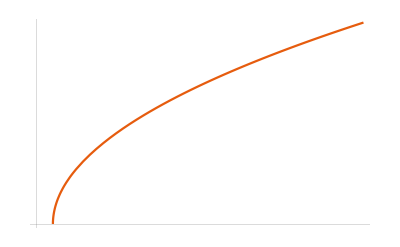

```mathematica
Plot[√(2 x-1),{x,0,10},PlotTheme->"Scientific",Frame->{{Automatic,None},{Automatic,None}}]
```

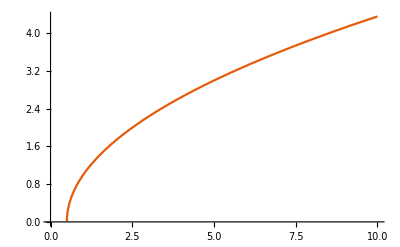

```mathematica
Show[%11,Axes->True]
```

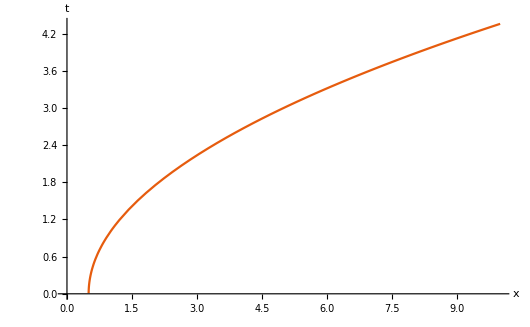

```mathematica
Show[%12,AxesLabel->{HoldForm[x],HoldForm[t]},PlotLabel->None,LabelStyle->{FontFamily->"Palatino",GrayLevel[0]}]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S2, PDEs/images/characteristic_curve.pdf",%13,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S2, PDEs/images/characteristic_curve.pdf

```mathematica
Plot[√(2 x-1),{x,0,10},PlotTheme->"Scientific"]
```

-Graphics-

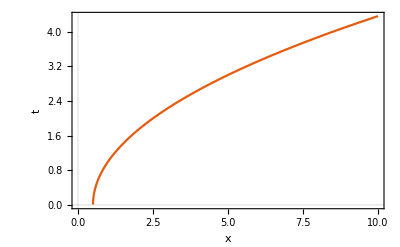

```mathematica
Show[%7,AxesLabel->{HoldForm[x],HoldForm[t]},PlotLabel->None,LabelStyle->{FontFamily->"Palatino",GrayLevel[0]}]
```

```mathematica
Inverse[{{1,Sin[a+b]},{Sin[a+b],1}}]
Simplify[%]
Inverse[{{1,Cos[p]},{Cos[p],1}}]
Simplify[%]
```

{{-1/(-1+Sin[a+b]^2),Sin[a+b]/(-1+Sin[a+b]^2)},{Sin[a+b]/(-1+Sin[a+b]^2),-1/(-1+Sin[a+b]^2)}}

{{Sec[a+b]^2,-Sec[a+b] Tan[a+b]},{-Sec[a+b] Tan[a+b],Sec[a+b]^2}}

{{-1/(-1+Cos[p]^2),Cos[p]/(-1+Cos[p]^2)},{Cos[p]/(-1+Cos[p]^2),-1/(-1+Cos[p]^2)}}

{{Csc[p]^2,-Cot[p] Csc[p]},{-Cot[p] Csc[p],Csc[p]^2}}

```mathematica
{{-1/(-1+Cos[p]^2),Cos[p]/(-1+Cos[p]^2)},{Cos[p]/(-1+Cos[p]^2),-1/(-1+Cos[p]^2)}}
```

```mathematica
{{-1/(-1+Cos[p]^2),Cos[p]/(-1+Cos[p]^2)},{Cos[p]/(-1+Cos[p]^2),-1/(-1+Cos[p]^2)}}
```

{{-1/(-1+Cos[p]^2),Cos[p]/(-1+Cos[p]^2)},{Cos[p]/(-1+Cos[p]^2),-1/(-1+Cos[p]^2)}}

```mathematica
Inverse[{{-1/(-1+Cos[p]^2),Cos[p]/(-1+Cos[p]^2)},{Cos[p]/(-1+Cos[p]^2),-1/(-1+Cos[p]^2)}}]
```

{{1,Cos[p]},{Cos[p],1}}

```mathematica
Simplify[%]
```

{{1,Cos[p]},{Cos[p],1}}

```mathematica
Integrate[Sin[x]^2,{x,0,Pi}]
```

π/2

```mathematica
LegendreP[3,x]
```

1/2 (-3 x+5 x^3)

Set::write: Tag Times in (√(2/π) Sinc[ω])[ω_] is Protected.

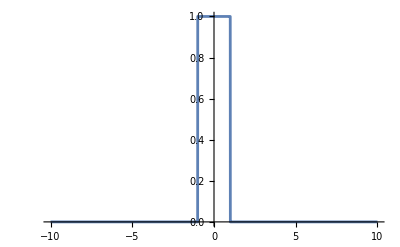

-Graphics-

```mathematica
fhat[ω_] = FourierTransform[UnitBox[t/2],t,ω];
Plot[UnitBox[t/2],{t,-10,10},Exclusions->None]
Plot[fhat[ω],{ω,-10,10}]
```

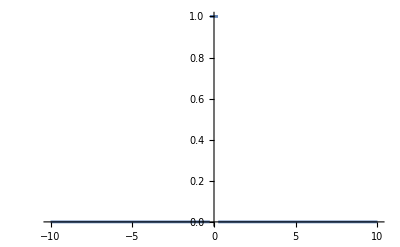

```mathematica
g = UnitBox[2x];
ghat= FourierTransform[UnitBox[2x],x,k];
Plot[g,{x,-10,10}]
```

```mathematica
Integrate[(Sin[x]^2)/(x^2),{x,-Infinity,Infinity}]
```

π

```mathematica
Integrate[(1/Pi)*(3*Cos[n*x]-2x*Cos[n*x]),{x,-Pi,Pi}]
```

(6 Sin[n π])/(n π)

```mathematica
Integrate[(1/Pi)*(3-2x),{x,-Pi,Pi}]
```

6

```mathematica
Integrate[2x*Sin[n*x],{x,-Pi,Pi}]
```

(-4 n π Cos[n π]+4 Sin[n π])/n^2

```mathematica
Integrate[(1/Pi)*(3*Sin[n*x]-2x*Sin[n*x]),{x,-Pi,Pi}]
```

(4 n π Cos[n π]-4 Sin[n π])/(n^2 π)

```mathematica
Integrate[Cos[(n/2)*x]*Cos[x],{x,0,Pi/2}]
```

-(4 Cos[(n π)/4])/(-4+n^2)

```mathematica
Expand[Cos[n*Pi/4]]
```

Cos[(n π)/4]

```mathematica
Integrate[Sin[(n/2)*x]*Cos[x],{x,0,Pi/2}]
```

(2 (n-2 Sin[(n π)/4]))/(-4+n^2)

```mathematica
TrigExpand[(2 (n-2 Sin[(n π)/4]))/(-4+n^2)]
```

(2 n)/(-4+n^2)-(4 Sin[(n π)/4])/(-4+n^2)

```mathematica
∑_(n=1)^∞ ((2 n)/(-4+n^2)-(4 Sin[(n π)/4])/(-4+n^2))
```

∑_(n=1)^∞ ((2 n)/(-4+n^2)-(4 Sin[(n π)/4])/(-4+n^2))

```mathematica
Simplify[(2 n)/(-4+n^2)-(4 Sin[(n π)/4])/(-4+n^2)]
```

```mathematica
TrigReduce[(2 n)/(-4+n^2)-(4 Sin[(n π)/4])/(-4+n^2)]
```

(2 (n-2 Sin[(n π)/4]))/(-4+n^2)

```mathematica
FourierCoefficient[x^2,x,n]
```

Piecewise[{{π^2/3, n==0}, {(2 (-1)^n)/n^2, True}}]

Syntax::tsntxi: "∫_0^5 f(x) dx" is incomplete; more input is needed.

```mathematica
FourierCosCoefficient[Piecewise[{{0,-Pi/2<=x<0},{Cos[x],0<=x<Pi/2}}],x,n]
```

(2 Cos[(n π)/2])/(π-n^2 π)

What are the Fourier coefficients for the piecewise function defined as 0 between -Pi/2 and 0, and Cos[x] between 0 and Pi/2?

WolframAlphaQueryResults

```mathematica
Integrate[(Cos[x])^2,{x,0,Pi/2}]
```

π/4

```mathematica
Integrate[Sin[x]Cos[x],{x,0,Pi/2}]
```

1/2

```mathematica
1/Pi * Integrate[x^2*Cos[n*x],{x,0,Pi}]
```

(2 n π Cos[n π]+(-2+n^2 π^2) Sin[n π])/(n^3 π)

```mathematica
1/Pi * Integrate[x^2*Sin[n*x],{x,0,Pi}]
```

(-2+(2-n^2 π^2) Cos[n π]+2 n π Sin[n π])/(n^3 π)

```mathematica
Assuming[Mod[n,1]==0,
(1/Pi)*Integrate[x^2*Cos[n*x],{x,0,Pi}]*Cos[n*x] +
(1/Pi)*Integrate[x^2*Sin[n*x],{x,0,Pi}] * Sin[n*x]
]
```

(2 (-1)^n Cos[n x])/n^2+((-2+(-1)^n (2-n^2 π^2)) Sin[n x])/(n^3 π)

```mathematica
Integrate[x^2,{x,0,Pi}]
```

π^3/3

```mathematica
Assuming[Mod[n,1]==0,FourierCosSeries[x^2,x,5]]
```

π^2/3+4 (-Cos[x]+1/4 Cos[2 x]-1/9 Cos[3 x]+1/16 Cos[4 x]-1/25 Cos[5 x])

```mathematica
Assuming[Mod[n,1]==0,
Integrate[(2/Pi)*(x+1)*(Sin[n*x]),{x,0,Pi}]
]
```

-(2 (-1+(-1)^n+(-1)^n π))/(n π)

```mathematica
Assuming[Mod[n,1]==0,
Integrate[(x)*(2-x)*(Sin[(n*Pi/2)*x]),{x,0,2}]]
```

-(16 (-1+(-1)^n))/(n^3 π^3)

```mathematica
FourierTransform[Sin[5t],t,w]
```

ⅈ √(π/2) DiracDelta[-5+w]-ⅈ √(π/2) DiracDelta[5+w]

```mathematica
Assuming[Mod[n,1]==0, Integrate[x*Cos[(n*Pi*x)/2],{x,0,1}]]
```

(2 (-2+2 Cos[(n π)/2]+n π Sin[(n π)/2]))/(n^2 π^2)

```mathematica
Integrate[x*Exp[-x],x]
```

ⅇ^-x (-1-x)

```mathematica
DSolve[y''[t] + 2*B*y'[t] + (omega0^2)*y[t] == F0*Cos[omega*t],y,t]
```

{{y→Function[{t},ⅇ^((-B-√(B^2-omega0^2)) t) C[1]+ⅇ^((-B+√(B^2-omega0^2)) t) C[2]+(-F0 omega^2 Cos[omega t]+F0 omega0^2 Cos[omega t]+2 B F0 omega Sin[omega t])/(4 B^2 omega^2+omega^4-2 omega^2 omega0^2+omega0^4)]}}

```mathematica
D[D[F0*Exp[I*omega*t]*((-2*Sqrt[B^2-omega0^2])/(omega^2-omega0^2 + 2*I*B*omega)),t],t] + 2*B*D[F0*Exp[I*omega*t]*((-2*Sqrt[B^2-omega0^2])/(omega^2-omega0^2 + 2*I*B*omega)),t] + omega0^2*F0*Exp[I*omega*t]*((-2*Sqrt[B^2-omega0^2])/(omega^2-omega0^2 + 2*I*B*omega))
```

-(4 ⅈ B ⅇ^(ⅈ omega t) F0 omega √(B^2-omega0^2))/(2 ⅈ B omega+omega^2-omega0^2)+(2 ⅇ^(ⅈ omega t) F0 omega^2 √(B^2-omega0^2))/(2 ⅈ B omega+omega^2-omega0^2)-(2 ⅇ^(ⅈ omega t) F0 omega0^2 √(B^2-omega0^2))/(2 ⅈ B omega+omega^2-omega0^2)

```mathematica
Simplify[%]
```

-(2 ⅇ^(ⅈ omega t) F0 √(B^2-omega0^2) (2 B omega+ⅈ (omega^2-omega0^2)))/(2 B omega-ⅈ (omega^2-omega0^2))

```mathematica
Assuming[Mod[n,1]==0,2/a *Integrate[x*Cos[(n*Pi/a)*x],{x,0,a}]]
```

(2 (-1+(-1)^n) a)/(n^2 π^2)

```mathematica
Integrate[Sin[(n*Pi)y/a]*Sin[(m*Pi)z/a],{y,0,a},{z,0,a}]
```

(4 a^2 Sin[(m π)/2]^2 Sin[(n π)/2]^2)/(m n π^2)

```mathematica
N[BesselJZero[1,6]/BesselJZero[1,5]]
```

1.19096

```mathematica
Integrate[Exp[I*k*x]*Sin[x],{x,-Infinity,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(ⅈ k x) Sin[x] does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(ⅈ k x) Sin[x]ⅆx

```mathematica
Integrate[(1/6)*(t+1)*(Exp[-2x+2t]-Exp[4x-4t]),{t,0,x}]
```

1/96 (9-4 ⅇ^(-2 x)-5 ⅇ^(4 x)+12 x)

```mathematica
Integrate[(1/2)*(x-(t^2/x))*(Sin[t]),{t,0,x}]
```

(2+x^2-2 Cos[x]-2 x Sin[x])/(2 x)

```mathematica
(1/(2*Pi))Integrate[Exp[t]*Exp[-4k^2*t],{k,-Infinity,Infinity}]
```

ConditionalExpression[ⅇ^t/(4 √π √t), Re[t]>0]

```mathematica
K[x_,t_]=InverseFourierTransform[Exp[(1-4k^2)*t],k,x]
```

(ⅇ^(t-x^2/(16 t)))/(2 √2 √t)

```mathematica
Convolve[K[y,t],Sin[y],y,x]
```

ⅇ^(-3 t) √(2 π) √(1/t) √t Sin[x]

```mathematica
Tan[ArcTan[x]]
```

x

```mathematica
ArcTan[Tan[x]]
```

ArcTan[Tan[x]]